```mathematica
Quit
Clear[*]
```

```mathematica
data={{0,0},{1,3},{3,2},{5,2},{4,1},{10,-3}}
```

{{0,0},{1,3},{3,2},{5,2},{4,1},{10,-3}}

```mathematica
sp=Interpolation[data,InterpolationOrder->2]
```

InterpolatingFunction[…]

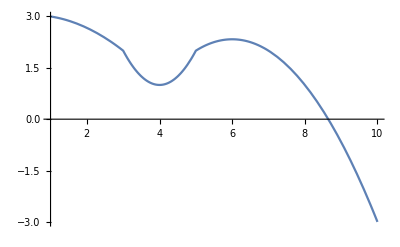

```mathematica
Plot[sp[x],{x,1,10}]
```

```mathematica
sp1=Interpolation[data,Method->"Spline"]
```

InterpolatingFunction[…]

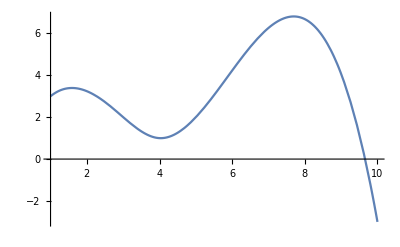

```mathematica
Plot[sp1[x],{x,1,10}]
```

```mathematica
sp2=Interpolation[data,Method->"Hermite"]
```

InterpolatingFunction[…]

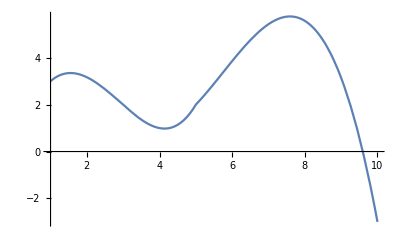

```mathematica
Plot[sp2[x], {x,1,10}]
```

```mathematica
c[x_]:=InterpolatingPolynomial[data,x]
```

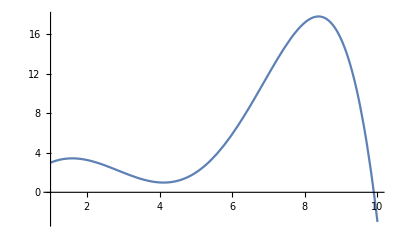

```mathematica
Plot[c[x], {x,1,10}]
```

```mathematica
Clear[*]
```

```mathematica
A={{1,2},{3,4}}
```

{{1,2},{3,4}}

```mathematica
A//MatrixForm
```

(1 | 2
3 | 4)

```mathematica
B={{5,6}}
```

{{5,6}}

```mathematica
B//MatrixForm
```

(5 | 6)

```mathematica
result=Transpose[Join[Transpose[A],B]]
```

{{1,2,5},{3,4,6}}

```mathematica
result//MatrixForm
```

(1 | 2 | 5
3 | 4 | 6)

```mathematica
clear[*]
```

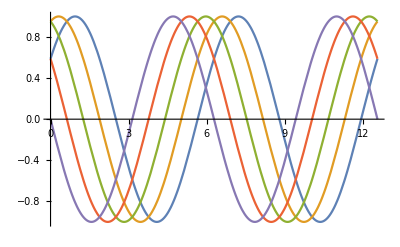

```mathematica
Plot[Evaluate[Table[Sin[x+a],{a,π/5,π,π/5}]],{x,0,4*π}]
```

```mathematica
Plot[Evaluate[Table[Sin[x+a],{a,π/5,π,π/5}]],{x,0,4*π},PlotLegends-> Automatic]
```

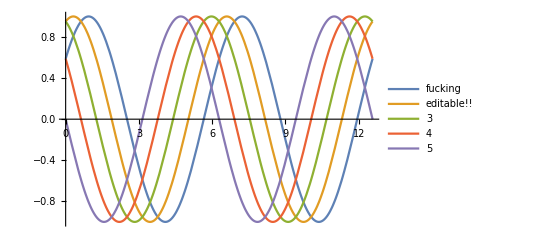

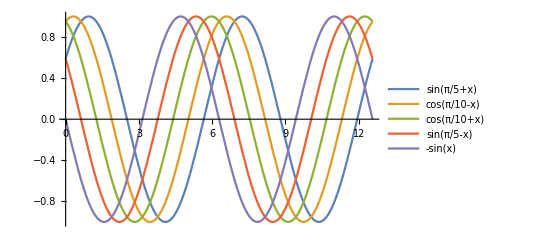

```mathematica
Plot[Evaluate[Table[Sin[x+a],{a,π/5,π,π/5}]],{x,0,4*π},PlotLegends-> "Expressions"]
```